```mathematica
Quit
```

The notebook presents numerical checks of the partially expanded analytic trajectories, implemented in the AnalyticSpinOrbitsHamiltonJacobi package, against numerical solutions of the equations of motion in first order form.  See arXiv:2603.04682  (https://arxiv.org/abs/2603.04682 )

PREREQUISITEs: the following package is needed
- KerrGeodesics from the BPToolkit. This package is needed to calculate the location of the geodesic separatrix.

If you make use of this notebook, please acknowledge 
- “Piovano”  (https://arxiv.org/abs/2603.04682 )
- KerrGeodesics package,  (https://zenodo.org/records/8108265 ) of the  BHPToolkit

Most of the plots are not saved to reduce the file of the notebook. Run all sections in order in each chapter to produce the plots.

### Convention for EoM

Here we follow the same convention of  CQG, Volume 37, Number 14  (https://iopscience.iop.org/article/10.1088/1361-6382/ab79d5 )

r_1== p/(1-e)
r_2== p/(1+e)
z_1==√(1-x^2)

or

p==2(r_1 r_2)/(r_1+r_2)
e== (r_1-r_2)/(r_1+r_2)
x ==  Sign[ℒ]√(1-z_1^2)

(circular) 0<e<1 (parabolic)
(retrograde) -1 < x < 1 (prograde)
p> p_LSO(e,x)

Equatorial orbits

x==±1
z_1==0
𝒬 ==0

“spar” and “sort” are the parallel and orthogonal component of the spin to the total angular momentum.

### Loading all the necessary files

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<KerrGeodesics`
```

```mathematica
Get["../AnalyticSpinOrbitsHamiltonJacobi.wl"]
```

## Generic plunge

## Regular gauge - prograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlunge=0.9`50;
S=1/2;
eccPlunge=0.7`50;
xPlungeBoundOrbit=1;
```

```mathematica
pPlunge=KerrGeoSeparatrix[aPlunge,eccPlunge,xPlungeBoundOrbit]-1/2
```

2.5782127178009769707291085222982272524218364585

```mathematica
rp=1+√(1-aPlunge^2);
rm=1-√(1-aPlunge^2);
```

```mathematica
Plunge=KerrEqFEPlungePartialExp[aPlunge,S,pPlunge,eccPlunge,xPlungeBoundOrbit];
```

```mathematica
r1=Plunge["r1"];
```

### Numerical solutions equations of motion vs analytic results

```mathematica
tODEPlunge=t/.First@NDSolve[{t'[r]==Plunge["dtdr"][r],t[r1-10^(-5)]==Plunge["tr"][r1-10^(-5)]},t,{r,rp+10^(-3),r1-10^(-5)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[tODEPlunge[r]-Plunge["tr"][r]],{r,rp+10^(-3),r1-10^(-5)},PlotRange->All]
```

```mathematica
ϕODEPlunge=ϕ/.First@NDSolve[{ϕ'[r]==Plunge["dϕdr"][r],ϕ[r1-10^(-5)]==Plunge["ϕr"][r1-10^(-5)]},ϕ,{r,rp+10^(-3),r1-10^(-5)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[ϕODEPlunge[r]-Plunge["ϕr"][r]],{r,rp+10^(-3),r1-10^(-5)},PlotRange->All]
```

## Regular gauge - retrograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlunge=0.9`50;
S=1/2;
eccPlunge=0.7`50;
xPlungeBoundOrbit=-1;
```

```mathematica
pPlunge=KerrGeoSeparatrix[aPlunge,eccPlunge,xPlungeBoundOrbit]-1/2
```

10.084693410815743456631284517627671373786056789

```mathematica
rp=1+√(1-aPlunge^2);
rm=1-√(1-aPlunge^2);
```

```mathematica
Plunge=KerrEqFEPlungePartialExp[aPlunge,S,pPlunge,eccPlunge,xPlungeBoundOrbit];
```

```mathematica
r1=Plunge["r1"];
```

### Numerical solutions equations of motion vs analytic results

```mathematica
tODEPlunge=t/.First@NDSolve[{t'[r]==Plunge["dtdr"][r],t[r1-10^(-5)]==Plunge["tr"][r1-10^(-5)]},t,{r,rp+10^(-3),r1-10^(-5)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[tODEPlunge[r]-Plunge["tr"][r]],{r,rp+10^(-3),r1-10^(-5)},PlotRange->All]
```

```mathematica
ϕODEPlunge=ϕ/.First@NDSolve[{ϕ'[r]==Plunge["dϕdr"][r],ϕ[r1-10^(-5)]==Plunge["ϕr"][r1-10^(-5)]},ϕ,{r,rp+10^(-3),r1-10^(-5)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[ϕODEPlunge[r]-Plunge["ϕr"][r]],{r,rp+10^(-3),r1-10^(-5)},PlotRange->All]
```

## Plunge related to periodic orbits

## Regular gauge - prograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlunge=0.9`50;
S=1/2;
eccPlunge=0.7`50;
xPlungeBoundOrbit=1;
```

```mathematica
pPlunge=KerrGeoSeparatrix[aPlunge,eccPlunge,xPlungeBoundOrbit]-1/2
```

2.5782127178009769707291085222982272524218364585

```mathematica
rp=1+√(1-aPlunge^2);
rm=1-√(1-aPlunge^2);
```

```mathematica
Plunge=KerrEqFEPlungePartialExp[aPlunge,S,pPlunge,eccPlunge,xPlungeBoundOrbit];
```

```mathematica
r1=Plunge["r1"];
```

### Numerical solutions equations of motion vs analytic results

```mathematica
tODEPlunge=t/.First@NDSolve[{t'[r]==Plunge["dtdr"][r],t[r1-10^(-5)]==Plunge["tr"][r1-10^(-5)]},t,{r,rp+10^(-3),r1-10^(-5)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[tODEPlunge[r]-Plunge["tr"][r]],{r,rp+10^(-3),r1-10^(-5)},PlotRange->All]
```

```mathematica
ϕODEPlunge=ϕ/.First@NDSolve[{ϕ'[r]==Plunge["dϕdr"][r],ϕ[r1-10^(-5)]==Plunge["ϕr"][r1-10^(-5)]},ϕ,{r,rp+10^(-3),r1-10^(-5)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[ϕODEPlunge[r]-Plunge["ϕr"][r]],{r,rp+10^(-3),r1-10^(-5)},PlotRange->All]
```

## Regular gauge - retrograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlungeBoundOrbit=0.9`50;
S=1/20;
eccPlungeBoundOrbit=0.35`50;
xPlungeBoundOrbit=-1;
```

```mathematica
pPlungeBoundOrbit=KerrGeoSeparatrix[aPlungeBoundOrbit,eccPlungeBoundOrbit,xPlungeBoundOrbit]+1;
```

```mathematica
rp=1+√(1-aPlungeBoundOrbit^2);
rm=1-√(1-aPlungeBoundOrbit^2);
```

```mathematica
PlungeBoundOrbit=KerrEqFEPlungeBoundOrbitPartialExp[aPlungeBoundOrbit,S,pPlungeBoundOrbit,eccPlungeBoundOrbit,1];
```

Starting point of plunges related to bound orbits: r_(3g)=2/(1-E_g^2)-(r_(1g)+r_(2g))

```mathematica
r3=PlungeBoundOrbit["r3"];
```

### Numerical solutions equations of motion vs analytic results

```mathematica
tODEPlungeBoundOrbit=t/.First@NDSolve[{t'[r]==PlungeBoundOrbit["dtdr"][r],t[r3-10^(-5)]==PlungeBoundOrbit["tr"][r3-10^(-5)]},t,{r,rp+10^(-3),r3-10^(-5)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[tODEPlungeBoundOrbit[r]-PlungeBoundOrbit["tr"][r]],{r,rp+10^(-3),r3-10^(-5)},PlotRange->All]
```

```mathematica
ϕODEPlungeBoundOrbit=ϕ/.First@NDSolve[{ϕ'[r]==PlungeBoundOrbit["dϕdr"][r],ϕ[r3-10^(-5)]==PlungeBoundOrbit["ϕr"][r3-10^(-5)]},ϕ,{r,rp+10^(-3),r3-10^(-5)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[ϕODEPlungeBoundOrbit[r]-PlungeBoundOrbit["ϕr"][r]],{r,rp+10^(-3),r3-10^(-5)},PlotRange->All]
```

## Critical plunge

## Regular gauge - prograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aCritplunge=0.9`50;
S=1/2;
eccCritplunge=0.45`50;
xCritplunge=1;
```

```mathematica
pCritplunge=KerrGeoSeparatrix[aCritplunge,eccCritplunge,xCritplunge]
```

2.77433156421648935787406408054133207855903537732

```mathematica
rp=1+√(1-aCritplunge^2);
rm=1-√(1-aCritplunge^2);
```

```mathematica
r1g=pCritplunge/(1-eccCritplunge);
r2g=pCritplunge/(1+eccCritplunge);
```

Critical plunge

```mathematica
AbsoluteTiming[Critplunge=KerrEqFECritplungePartialExp[aCritplunge,S,pCritplunge,eccCritplunge,xCritplunge];]
```

{0.000721,Null}

```mathematica
r1=Critplunge["r1"];
r2=Critplunge["r2"];
```

### Numerical solutions equations of motion vs analytic results

```mathematica
tODECritplunge=t/.First@NDSolve[{t'[r]==Critplunge["dtdr"][r],t[r2-10^(-3)]==Critplunge["tr"][r2-10^(-3)]},t,{r,rp+10^(-3),r2-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[tODECritplunge[r]-Critplunge["tr"][r]],{r,rp+10^(-3),r2-10^(-3)},PlotRange->All]
```

```mathematica
ϕODECritplunge=ϕ/.First@NDSolve[{ϕ'[r]==Critplunge["dϕdr"][r],ϕ[r2-10^(-3)]==Critplunge["ϕr"][r2-10^(-3)]},ϕ,{r,rp+10^(-3),r2-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[ϕODECritplunge[r]-Critplunge["ϕr"][r]],{r,rp+10^(-3),r2-10^(-3)},PlotRange->All]
```

### Plot to export

```mathematica
ϕODECritplunge0rm=ϕ/.First@NDSolve[{ϕ'[r]==Critplunge["dϕdr"][r],ϕ[rm-10^(-3)]==Critplunge["ϕr"][rm-10^(-3)]},ϕ,{r,10^(-2),rm-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
ϕODECritplungermrp=ϕ/.First@NDSolve[{ϕ'[r]==Critplunge["dϕdr"][r],ϕ[rm+10^(-3)]==Critplunge["ϕr"][rm+10^(-3)]},ϕ,{r,rm+10^(-3),rp-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
ϕODECritplungerprr2=ϕ/.First@NDSolve[{ϕ'[r]==Critplunge["dϕdr"][r],ϕ[r2-10^(-3)]==Critplunge["ϕr"][r2-10^(-3)]},ϕ,{r,rp+10^(-3),r2-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
plotdiffϕCritplunge0rm=LogPlot[Abs[Critplunge[ "ϕr"][r]-ϕODECritplunge0rm[r]],{r,10^(-2),rm-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,r2-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|ϕ_analytic^Critical-ϕ_num^Critical|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600];
```

```mathematica
plotdiffϕCritplungermrp=LogPlot[Abs[Critplunge[ "ϕr"][r]-ϕODECritplungermrp[r]],{r,rm+10^(-3),rp-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,r2-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|ϕ_analytic^Critical-ϕ_num^Critical|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600];
```

```mathematica
plotdiffϕCritplungerpr2=LogPlot[Abs[Critplunge[ "ϕr"][r]-ϕODECritplungerprr2[r]],{r,rp+10^(-3),r2-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,r2-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|ϕ_analytic^Critical-ϕ_num^Critical|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600];
```

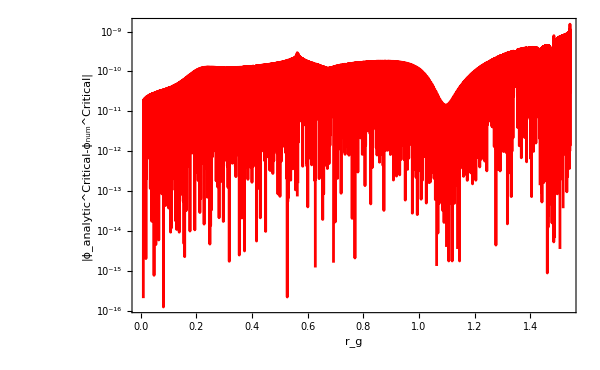

```mathematica
plotdiffϕCritplunge=Show[plotdiffϕCritplunge0rm,plotdiffϕCritplungermrp,plotdiffϕCritplungerpr2]
```

## Regular gauge - retrograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aCritplunge=0.9`50;
S=1/2;
eccCritplunge=0.45`50;
xCritplunge=-1;
```

```mathematica
pCritplunge=KerrGeoSeparatrix[aCritplunge,eccCritplunge,xCritplunge]
```

9.94962412521538647758316932741738178793769289441

```mathematica
rp=1+√(1-aCritplunge^2);
rm=1-√(1-aCritplunge^2);
```

```mathematica
r1g=pCritplunge/(1-eccCritplunge);
r2g=pCritplunge/(1+eccCritplunge);
```

Critical plunge

```mathematica
AbsoluteTiming[Critplunge=KerrEqFECritplungePartialExp[aCritplunge,S,pCritplunge,eccCritplunge,xCritplunge];]
```

{0.000455,Null}

```mathematica
r1=Critplunge["r1"];
r2=Critplunge["r2"];
```

### Numerical solutions equations of motion vs analytic results

```mathematica
tODECritplunge=t/.First@NDSolve[{t'[r]==Critplunge["dtdr"][r],t[r2-10^(-3)]==Critplunge["tr"][r2-10^(-3)]},t,{r,rp+10^(-3),r2-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[tODECritplunge[r]-Critplunge["tr"][r]],{r,rp+10^(-3),r2-10^(-3)},PlotRange->All]
```

```mathematica
ϕODECritplunge=ϕ/.First@NDSolve[{ϕ'[r]==Critplunge["dϕdr"][r],ϕ[r2-10^(-3)]==Critplunge["ϕr"][r2-10^(-3)]},ϕ,{r,rp+10^(-3),r2-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[ϕODECritplunge[r]-Critplunge["ϕr"][r]],{r,rp+10^(-3),r2-10^(-3)},PlotRange->All]
```

## ISCO plunge

## Regular gauge - prograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aISCOplunge=0.9`45;
S=1/2;
xISCOplunge=1;
```

```mathematica
rp=1+√(1-aISCOplunge^2);
rm=1-√(1-aISCOplunge^2);
```

```mathematica
r1g=KerrGeoSeparatrix[aISCOplunge,0,xISCOplunge]
```

2.320883041761887246790086191922686088978602

ISCO plunge

```mathematica
AbsoluteTiming[ISCOplunge=KerrEqISCOPlungePartialExp[aISCOplunge,S,xISCOplunge];]
```

{0.000374,Null}

```mathematica
rISCO=ISCOplunge["rISCO"]
```

1.7836354036548365169756524317085287131303

### Numerical solutions equations of motion vs analytic results

```mathematica
tODEISCOplunge=t/.First@NDSolve[{t'[r]==ISCOplunge["dtdr"][r],t[rISCO-10^(-3)]==ISCOplunge["tr"][rISCO-10^(-3)]},t,{r,rp+10^(-3),rISCO-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[tODEISCOplunge[r]-ISCOplunge["tr"][r]],{r,rp+10^(-3),rISCO-10^(-3)},PlotRange->All]
```

```mathematica
ϕODEISCOplunge=ϕ/.First@NDSolve[{ϕ'[r]==ISCOplunge["dϕdr"][r],ϕ[rISCO-10^(-3)]==ISCOplunge["ϕr"][rISCO-10^(-3)]},ϕ,{r,rp+10^(-3),rISCO-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[ϕODEISCOplunge[r]-ISCOplunge["ϕr"][r]],{r,rp+10^(-3),rISCO-10^(-3)},PlotRange->All]
```

### Plot to export

```mathematica
ϕODEISCOplunge0rm=ϕ/.First@NDSolve[{ϕ'[r]==ISCOplunge["dϕdr"][r],ϕ[rm-10^(-3)]==ISCOplunge["ϕr"][rm-10^(-3)]},ϕ,{r,10^(-2),rm-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
ϕODEISCOplungermrp=ϕ/.First@NDSolve[{ϕ'[r]==ISCOplunge["dϕdr"][r],ϕ[rm+10^(-3)]==ISCOplunge["ϕr"][rm+10^(-3)]},ϕ,{r,rm+10^(-3),rp-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
ϕODEISCOplungerprISCO=ϕ/.First@NDSolve[{ϕ'[r]==ISCOplunge["dϕdr"][r],ϕ[rISCO-10^(-3)]==ISCOplunge["ϕr"][rISCO-10^(-3)]},ϕ,{r,rp+10^(-3),rISCO-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
plotdiffϕISCO0rm=LogPlot[Abs[ISCOplunge[ "ϕr"][r]-ϕODEISCOplunge0rm[r]],{r,10^(-2),rm-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,rISCO-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|ϕ_analytic^ISCO-ϕ_num^ISCO|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600];
```

```mathematica
plotdiffϕISCOrmrp=LogPlot[Abs[ISCOplunge[ "ϕr"][r]-ϕODEISCOplungermrp[r]],{r,rm+10^(-3),rp-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,rISCO-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|ϕ_analytic^ISCO-ϕ_num^ISCO|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600];
```

```mathematica
plotdiffϕISCOrprISCO=LogPlot[Abs[ISCOplunge[ "ϕr"][r]-ϕODEISCOplungerprISCO[r]],{r,rp+10^(-3),rISCO-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,rISCO-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|ϕ_analytic^ISCO-ϕ_num^ISCO|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600];
```

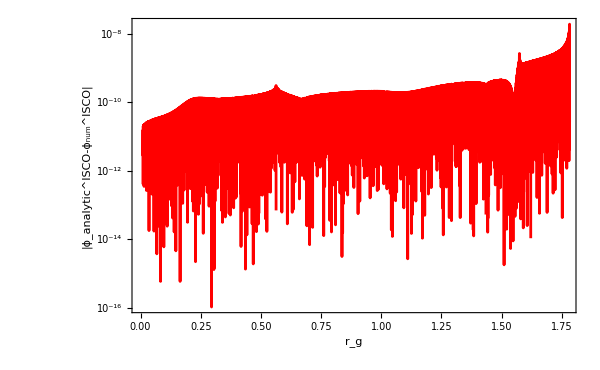

```mathematica
plotdiffϕISCO=Show[plotdiffϕISCO0rm,plotdiffϕISCOrmrp,plotdiffϕISCOrprISCO]
```

## Regular gauge - retrograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aISCOplunge=0.9`45;
S=1/2;
xISCOplunge=-1;
```

```mathematica
rp=1+√(1-aISCOplunge^2);
rm=1-√(1-aISCOplunge^2);
```

```mathematica
r1g=KerrGeoSeparatrix[aISCOplunge,0,xISCOplunge]
```

8.717352279606489315950123122494743539714513

ISCO plunge

```mathematica
AbsoluteTiming[ISCOplunge=KerrEqISCOPlungePartialExp[aISCOplunge,S,xISCOplunge];]
```

{0.000387,Null}

```mathematica
rISCO=ISCOplunge["rISCO"]
```

7.833479255135371893975825650967220008742678

### Numerical solutions equations of motion vs analytic results

```mathematica
tODEISCOplunge=t/.First@NDSolve[{t'[r]==ISCOplunge["dtdr"][r],t[rISCO-10^(-3)]==ISCOplunge["tr"][rISCO-10^(-3)]},t,{r,rp+10^(-3),rISCO-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[tODEISCOplunge[r]-ISCOplunge["tr"][r]],{r,rp+10^(-3),rISCO-10^(-3)},PlotRange->All]
```

```mathematica
ϕODEISCOplunge=ϕ/.First@NDSolve[{ϕ'[r]==ISCOplunge["dϕdr"][r],ϕ[rISCO-10^(-3)]==ISCOplunge["ϕr"][rISCO-10^(-3)]},ϕ,{r,rp+10^(-3),rISCO-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[ϕODEISCOplunge[r]-ISCOplunge["ϕr"][r]],{r,rp+10^(-3),rISCO-10^(-3)},PlotRange->All]
```